```mathematica
<<"C:\\Users\\aliha\\Desktop\\UNET\\UNET.m";
dirimg="C:\\Users\\aliha\\Downloads\\fabrice-ali\\deeplearning\\data\\train\\train_images_8bit"; 
dirmasks="C:\\Users\\aliha\\Downloads\\fabrice-ali\\deeplearning\\data\\train\\train_masks";
```

```mathematica
nNet=UNET
```

NetGraph[<>]

```mathematica
{dat,validationdata,hidden}=dataPrep[dirimg,dirmasks];
```

```mathematica
nNetInfo=trainNet[nNet,Join[First@dat,First@validationdata],Join[Last@dat,Last@validationdata]]
```

NetTrainResultsObject[<>]

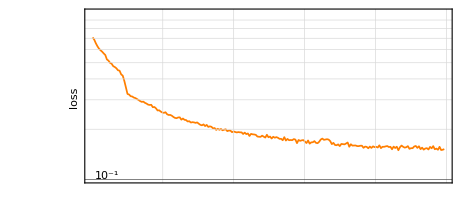

```mathematica
nNetInfo["LossEvolutionPlot"]
```

```mathematica
nNetTrained=nNetInfo["TrainedNet"]
```

NetGraph[<>]

```mathematica
img=hidden[[1,2]]
```

-Graphics-

```mathematica
{img,#,HighlightImage[img,MorphologicalPerimeter@Binarize@#]}&[ImageResize[nNetTrained[img,TargetDevice-> "GPU"],{168,168}]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
measureModelAccuracy[nNetTrained,First@hidden,Last@hidden]
```

{0.967268,1 | 0.950039
2 | 0.986445
3 | 0.974648
4 | 0.986133
5 | 0.966172
6 | 0.969414
7 | 0.966953
8 | 0.965938
9 | 0.978906
10 | 0.914609
11 | 0.944492
12 | 0.962148
13 | 0.966523
14 | 0.970156
15 | 0.987852
16 | 0.982344
17 | 0.962852
18 | 0.979492
19 | 0.968438
20 | 0.961797}

## with validation set

```mathematica
nNetInfo=trainNetwithValidation[nNet,First@dat,Last@dat,First@validationdata,Last@validationdata]
```

NetTrainResultsObject[<>]

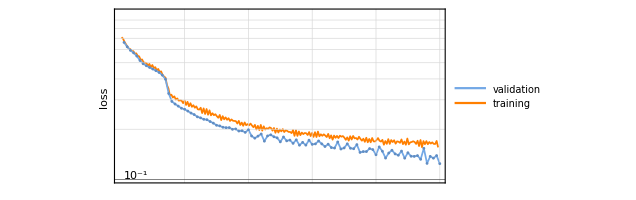

```mathematica
nNetInfo["LossEvolutionPlot"]
```

```mathematica
nNetTrained=nNetInfo["TrainedNet"]
```

NetGraph[<>]

```mathematica
img=hidden[[1,2]]
```

-Graphics-

```mathematica
{img,#,HighlightImage[img,MorphologicalPerimeter@Binarize@#]}&[ImageResize[nNetTrained[img,TargetDevice-> "GPU"],{168,168}]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
measureModelAccuracy[nNetTrained,First@hidden,Last@hidden]
```

{0.964963,1 | 0.940313
2 | 0.988359
3 | 0.965469
4 | 0.987617
5 | 0.967617
6 | 0.967266
7 | 0.963281
8 | 0.968555
9 | 0.973594
10 | 0.926484
11 | 0.952148
12 | 0.957695
13 | 0.960234
14 | 0.966719
15 | 0.987305
16 | 0.975664
17 | 0.957344
18 | 0.971406
19 | 0.970039
20 | 0.952148}